```mathematica
h[x_]:=Piecewise[{{1+c01 x+c02 x^2, 0≤x≤1/2}, {c11(x-1)+c12(x-1)^2, 1/2<x≤3/2}, {0, True}}];
f[x_]:=h[Abs[x]];
```

```mathematica
(*Continuity*)
C1l=Simplify[h[x],0≤x≤1/2]/.x->1/2
C1r=Simplify[h[x],1/2<x≤3/2]/.x->1/2
C2l=Simplify[h[x],1/2<x≤3/2]/.x->3/2
```

1+c01/2+c02/4

1/2 (-c11+c12/2)

1/2 (c11+c12/2)

```mathematica
(*Partition of unity and gradient representation*)
T0=CoefficientList[FullSimplify[∑_(i=-3)^3 f[x-i],x>0&&x<1/2],x]
T1=CoefficientList[FullSimplify[∑_(i=-3)^3 i f[x-i],x>0&&x<1/2],x]
```

{1,c01,c02+2 c12}

{0,-2 c11}

```mathematica
GenSols=Solve[{
	C1l==C1r,
	C2l==0,
	T0[[2]]==0,
	T0[[3]]==0,
	T1[[2]]==1
	},
	{c01,c02,c11,c12}
]
```

{{c01→0,c02→-2,c11→-1/2,c12→1}}

```mathematica
h[x]/.GenSols[[1]]
```

Piecewise[{{1-2 x^2, 0≤x≤1/2}, {(1-x)/2+(-1+x)^2, 1/2<x≤3/2}, {0, True}}]

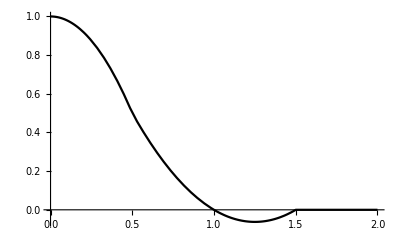

```mathematica
Plot[h[x]/.GenSols[[1]],{x,0,2},PlotStyle->Black]
```

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
W1[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF1=∑_(i=-5)^6 ∑_(j=-5)^6 W1[i-j]f[x-i,y-j]/.GenSol;
```

```mathematica
{SumF1a1,SumF1a2,SumF1a3,SumF1a4,SumF1a5,SumF1a6}=Parallelize[{
	Simplify[SumF1,x>0-1/2&&x<1-1/2&&y>0-1/2&&y<1-1/2],
	Simplify[SumF1,x>0-1/2&&x<1-1/2&&y>1-1/2&&y<2-1/2],
	Simplify[SumF1,x>-1-1/2&&x<0-1/2&&y>1-1/2&&y<2-1/2],
	Simplify[SumF1,x>-1-1/2&&x<0-1/2&&y>2-1/2&&y<3-1/2],
	Simplify[SumF1,x>-2-1/2&&x<-1-1/2&&y>2-1/2&&y<3-1/2],
	Simplify[SumF1,x>-2-1/2&&x<-1-1/2&&y>3-1/2&&y<4-1/2]
}];
{SumF1b1,SumF1b2,SumF1b3,SumF1b4,SumF1b5,SumF1b6}=Parallelize[{
	Simplify[SumF1,x>1-1/2&&x<2-1/2&&y>0-1/2&&y<1-1/2],
	Simplify[SumF1,x>1-1/2&&x<2-1/2&&y>-1-1/2&&y<0-1/2],
	Simplify[SumF1,x>2-1/2&&x<3-1/2&&y>-1-1/2&&y<0-1/2],
	Simplify[SumF1,x>2-1/2&&x<3-1/2&&y>-2-1/2&&y<-1-1/2],
	Simplify[SumF1,x>3-1/2&&x<4-1/2&&y>-2-1/2&&y<-1-1/2],
	Simplify[SumF1,x>3-1/2&&x<4-1/2&&y>-3-1/2&&y<-2-1/2]
}];
```

```mathematica
TableForm[{SumF1a1,SumF1a2,SumF1a3,SumF1a4,SumF1a5,SumF1a6}]
TableForm[{SumF1b1,SumF1b2,SumF1b3,SumF1b4,SumF1b5,SumF1b6}]
```

1/4 (2 φ^2+y^2 (2+4 φ-6 φ^2)+y (-1-2 φ+φ^2)+x (1+2 φ+2 y^2 (-2+φ) φ-φ^2+y (-1+φ^2))+2 x^2 (1+2 φ-y (-2+φ) φ-3 φ^2+2 y^2 (-1-4 φ+5 φ^2)))
1/8 (-2 (-1+2 x^2) (3-5 y+2 y^2) φ^2-2 x (1+2 x) (1-4 y+2 y^2) φ^2-x (1+2 x) (3-5 y+2 y^2) (-1-2 φ+φ^2))
1/8 (3+5 x+2 x^2) (3-5 y+2 y^2) φ^2
0
0
0

1/4 (-2 y φ+φ (-4+5 φ)+y^2 (2+16 φ-16 φ^2)+x^2 (2 φ (-4+3 φ)-4 y^2 φ (-6+5 φ)-2 y (-1+φ^2))+x (2+16 φ-13 φ^2+y (-4+2 φ+3 φ^2)+y^2 (-2-48 φ+42 φ^2)))
1/8 (2-24 φ+21 φ^2+y^2 (4-32 φ+22 φ^2)+y (4-68 φ+49 φ^2)+2 x^2 (2-16 φ+11 φ^2+2 y^2 (2-8 φ+5 φ^2)+y (8-36 φ+23 φ^2))-x (4-68 φ+49 φ^2+5 y (6-32 φ+21 φ^2)+2 y^2 (8-36 φ+23 φ^2)))
1/8 (9 x (3+5 y+2 y^2) (-1+φ)^2-2 x^2 (3+5 y+2 y^2) (-1+φ)^2-2 (11+25 y (-1+φ)^2+10 y^2 (-1+φ)^2-30 φ+15 φ^2))
1
1
1

```mathematica
{DSumF1a1,DSumF1a2,DSumF1a3,DSumF1b1,DSumF1b2,DSumF1b3}=Parallelize[{
	FullSimplify[D[SumF1a1,{{x,y}}]],
	FullSimplify[D[SumF1a2,{{x,y}}]],
	FullSimplify[D[SumF1a3,{{x,y}}]],
	FullSimplify[D[SumF1b1,{{x,y}}]],
	FullSimplify[D[SumF1b2,{{x,y}}]],
	FullSimplify[D[SumF1b3,{{x,y}}]]
}];
DSumF1a1=Simplify[DSumF1a1/.φ->1/2];
DSumF1a2=Simplify[DSumF1a2/.φ->1/2];
DSumF1a3=Simplify[DSumF1a3/.φ->1/2];
DSumF1b1=Simplify[DSumF1b1/.φ->1/2];
DSumF1b2=Simplify[DSumF1b2/.φ->1/2];
DSumF1b3=Simplify[DSumF1b3/.φ->1/2];
```

```mathematica
{Err1a1,Err1a2,Err1a3}=Parallelize[{
	Simplify[∫_(0-1/2)^(1-1/2) ∫_(0-1/2)^(1-1/2) (DSumF1a1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(1-1/2)^(2-1/2) ∫_(0-1/2)^(1-1/2) (DSumF1a2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(1-1/2)^(2-1/2) ∫_(-1-1/2)^(0-1/2) (DSumF1a3.{1,1})^2 ⅆxⅆy]
}];
{Err1b1,Err1b2,Err1b3}=Parallelize[{
	Simplify[∫_(0-1/2)^(1-1/2) ∫_(1-1/2)^(2-1/2) (DSumF1b1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-1-1/2)^(0-1/2) ∫_(1-1/2)^(2-1/2) (DSumF1b2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-1-1/2)^(0-1/2) ∫_(2-1/2)^(3-1/2) (DSumF1b3.{1,1})^2 ⅆxⅆy]
}];
```

```mathematica
Err1=FullSimplify[Err1a1+Err1a2+Err1a3+Err1b1+Err1b2+Err1b3]
N[Err1]
```

1061/4608

0.230252